System defined

NDSolve`Iterate::evcvmit: -- Message text not found -- (r) (1.42263×10^6) (1.42263×10^6) (100)

-Graphics-

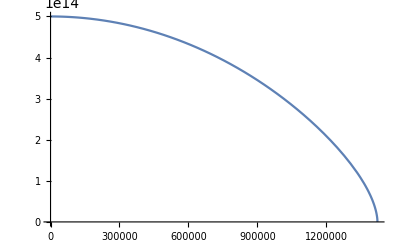

-Graphics-

Radius=1.42263×10^6

Mass=3.00588×10^33

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
G:=6.6742*10^(-8);
c:=2.99792458*10^(10);
(*G:=1;
c:=1;*)
γ:=2.75;
K:=1.982*10^(-6);
ρc:=5.0*10^(14);
(*γ:=0.3;
K:=1;
ρc:=1;*)
pc:=K*ρc^(γ);
r0:=0;
rSwitch:=10^(-6)

ρ[r_]=d[r];
p[r_]=K*(d[r])^(γ);
(*ϵ[r_]=p[r]/((γ-1)ρ[r])*)
ϵ[r_]=0;

eqnM:={m'[r]==4 π r^2 ρ[r](1+ϵ[r]/(c^2))};
condM:={m[r0]==0};

eqnP:={-p'[r]==Piecewise[{{G*(ρ[r]*(1+ϵ[r]/(c^2))+p[r]/(c^2))*(4 π* r*p[r]/(c^2)),r≤rSwitch},{G*(ρ[r]*(1+ϵ[r]/(c^2))+p[r]/(c^2))*(m[r]+4 π* r^3 *p[r]/(c^2))/(r^2*(1-2 *G* m[r]/(r*c^2))),r>rSwitch}}]};
condP:={p[r0]==pc};
condρ:={ρ[r0]==ρc};
stopCond:={WhenEvent[Evaluate[Re[d[r]]≤ρc/10000],rMax=r;"StopIntegration"]}

system:=Join[eqnM,eqnP,condM,condρ,stopCond];
Print["System defined"];
state=First[NDSolve`ProcessEquations[system, {m,d}, {r, r0, ∞}]];
NDSolve`Iterate[state,∞]
sol=NDSolve`ProcessSolutions[state];

Plot[Evaluate[m[r]/.sol],{r,r0,rMax},PlotRange->All]
Plot[Evaluate[d[r]/.sol],{r,r0,rMax},PlotRange->All]
Plot[Evaluate[p[r]/.sol],{r,r0,rMax},PlotRange->All]
Print["Radius=",rMax,""];
MStar:=Evaluate[m[rMax]/.sol];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
```

```mathematica
eqnΦ:={-Φ'[r]==Piecewise[{{(4 π* r*Evaluate[p[r]/.sol]/(c^2)),r≤rSwitch},{(Evaluate[m[r]/.sol]+4 π* r^3 *Evaluate[p[r]/.sol]/(c^2))/(r^2*(1-2 *G* Evaluate[m[r]/.sol]/(r*c^2))),r>rSwitch}}]};
condΦ:={Φ[Rmax]==1/2 ln[1-2*G*MStar/(rMax*c^2)]};
systemΦ:=Join[eqnΦ, condΦ];

(*stateΦ=First[NDSolve`ProcessEquations[systemΦ, {Φ}, {r, rMax, r0}]];
NDSolve`Iterate[stateΦ,∞]
solΦ=NDSolve`ProcessSolutions[stateΦ];*)
solΦ=NDSolve[systemΦ, {Φ}, {r, rMax, r0}]
Plot[Evaluate[Φ[r]/.solΦ],{r,r0,rMax},PlotRange->All]
```

NDSolve::ndsv: Cannot find starting value for the variable Φ.

NDSolve[{-Φ'[r]==(Piecewise[{{2.77123×10^-26 r (6
InterpolatingFunction[{{0., 1.42263 10 }}, <>][r])^2.75, r≤1/1000000}, {(                                      6
InterpolatingFunction[{{0., 1.42263 10 }}, <>][r]+2.77123×10^-26 r^3 (6
InterpolatingFunction[{{0., 1.42263 10 }}, <>][r])^2.75)/(r^2 (1-(1.48521×10^-28                                       6
InterpolatingFunction[{{0., 1.42263 10 }}, <>][r])/r)), r>1/1000000}, {0, True}}]),Φ[Rmax]==ln[0.686189]/2},{Φ},{r,1.42263×10^6,0}]

ReplaceAll::reps: {NDSolve[{-SuperscriptBox["Φ", "′", Rule[MultilineFunction, None]][r] == (TagBox[GridBox[{{"{", GridBox[{{Times[« 3 »], LessEqual[« 2 »]}, {Times[« 3 »], Greater[« 2 »]}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]]), Φ[Rmax] == ln[0.686189]/2}, {Φ}, {r, 1.42263×10^6, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 29.0622 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{-SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 29.0622 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{-1.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 29062.3 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-